## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/Poster colloque Bouyssy/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
green=RGBColor["#218b00"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->False,FrameStyle->st,PlotRange->All];
```

## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* for a string of an even number of A and B, replace every couple by the corresponding arrow *)
ToArrowAlphabet[string_]:=StringReplace[string,{"AB"->"R","BA"->"L","AA"->"Ia","BB"->"Ib"}];
(* return the vector counting the number of arrows *)
ArrowCountVec[string_]:=StringCount[string,#]&/@{"R","L","Ia","Ib"};
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

For the E=0 level to exist, we need an odd number of letters. But we also need the system to be bipartite for the wavefunction to be nonzero only on one site over two → open boundary conditions.

```mathematica
(* open approximant of a sequence seq of two letters, in normal numbering *)
ho[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

## Fibo arrows and heights

```mathematica
infl[seed_,l_]:=Nest[StringReplace[#,{"A"->"AB","B"->"A"}]&,seed,l];
inflAt[seed_,l_]:=Nest[StringReplace[#,{"A"->"ABABA","B"->"ABA"}]&,seed,l];
```

Consider the following counting function acting on the word W = W_0 W_1...:
 f_W(j) = Σ_(i=0→j)g(W_i W_(i+1)) with g(AB)=1, g(BA)=-1, g(AA)=0. 
 If W is a Fibonacci word, it is an almost periodic function.

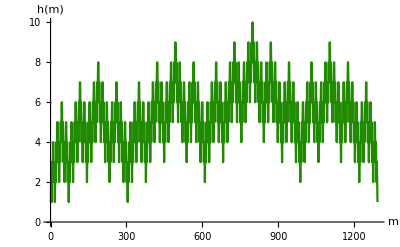

```mathematica
seq=inflAt["AB",5];
sub1=StringPartition[seq,2];
sub1=sub1/.{"AB"->1,"BA"->-1,"AA"->0};
tbl=Table[Total [sub1[[;;i]]],{i,Length[sub1]}];
ListPlot[%,PlotRange->All,Filling->None,Joined->True,AxesLabel->{"m","h(m)"},PlotStyle->{green}]
Export[NotebookDirectory[]<>"heights.pdf",%];
```

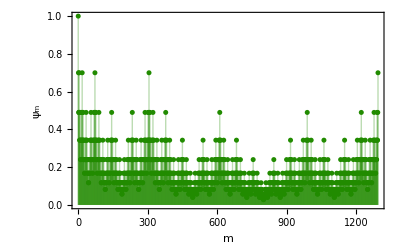

```mathematica
wf={1}~Join~(0.7^tbl);
ListPlot[wf,PlotRange->All,Frame->True,Filling->Axis,FrameLabel->stylize/@{"m","ψ_m"},PlotStyle->{green,PointSize[0.009]}]
Export[NotebookDirectory[]<>"wavefunction.pdf",%];
```

## Ag substitution

```mathematica
AgSub[l_,C0_String]:=Sub[{"A"->"ABA","B"->"A"},C0,l];
(* the field of arrows *)
AgArrows[l_]:=StringPartition[AgSub[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
```

```mathematica
AgSub[4,"B"]
```

ABAAABAABAABAAABA

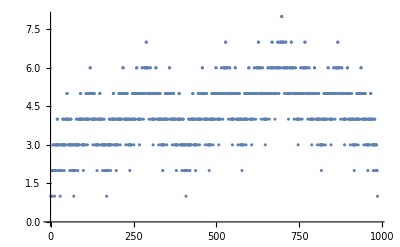

```mathematica
arrows=AgArrows[8];
AgHeights=Heights[arrows];
(* the height function goes to 0 arbitrarily far from the origin *)
ListPlot[AgHeights,PlotRange->All]
```

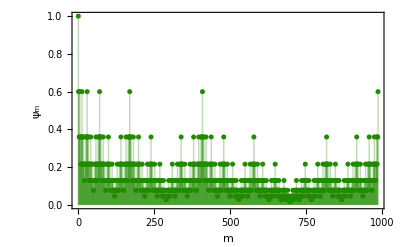

```mathematica
wf={1}~Join~(0.6^AgHeights);
ListPlot[wf,PlotRange->All,Frame->True,Filling->Axis,FrameLabel->stylize/@{"m","ψ_m"},PlotStyle->{green,PointSize[0.009]}]
Export[NotebookDirectory[]<>"wavefunction.pdf",%];
```

```mathematica
AgMaxs=MaxHeights[AgHeights];
```

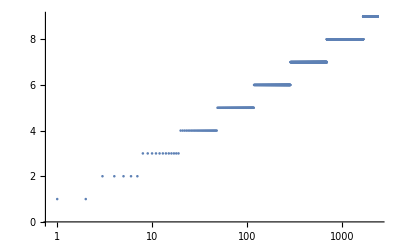

```mathematica
(* the height max grows logarithmically! *)
ListLogLinearPlot[AgMaxs,PlotRange->All]
```

```mathematica
mat=ho[ρ,AgSub[9,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

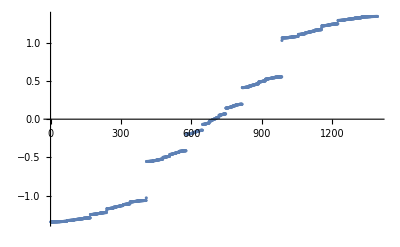

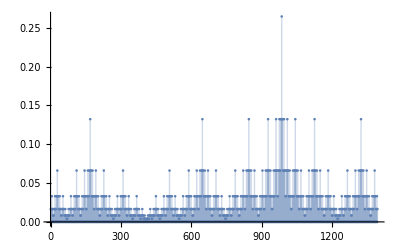

```mathematica
ListPlot[vals]
idxCenter=(Length[vals]+1)/2;
ListPlot[Abs@vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```